```mathematica
F=
(1+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)])/.{nuplus->vs+1/2 q,numin->vs-1/2 q}//Simplify;
SeriesCoefficient[F,{q,0,-2}]
SeriesCoefficient[F,{q,0,0}]
```

0

1/4 (8-2 vs Log[(1+vs)/(-1+vs)])

0

1+σ+1/2 (-1+σ) (-2+vs Log[(1+vs)/(-1+vs)])

1/2 (4-Log[2/(-1+vs)]+σ Log[2/(-1+vs)])+O[vs-1]^1

{ConditionalExpression[ⅇ^(4/(-1+σ)) (2+ⅇ^(-4/(-1+σ))), -π<-4 Im[1/(-1+σ)]≤π]}

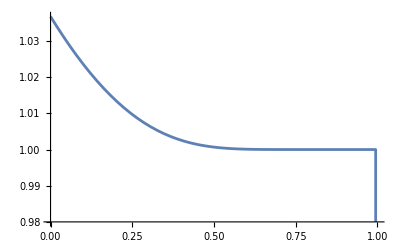

{ConditionalExpression[(2+ⅇ^4)/ⅇ^4-(8 σ)/ⅇ^4+O[σ]^2, -π<-4 Im[1/(-1+σ)]≤π]}

```mathematica
FΔ=
(1 (1+σ)+(1-σ)(1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)]))/.{nuplus->vs+1/2 q,numin->vs-1/2 q}//Simplify;
SeriesCoefficient[FΔ,{q,0,-2}]
SeriesCoefficient[FΔ,{q,0,0}]
Series[%,{vs,1,0}]
vsσ=SolveValues[(%//Normal)==0,vs]
Plot[vsσ[[1]],{σ,0,1}]
Series[vsσ,{σ,0,1}]
```

```mathematica
SeriesCoefficient[FΔ,{q,0,0}]
Series[%,{σ,0,1}]
```

1+σ+1/2 (-1+σ) (-2+vs Log[(1+vs)/(-1+vs)])

1/2 (4-vs Log[(1+vs)/(-1+vs)])+1/2 vs Log[(1+vs)/(-1+vs)] σ+O[σ]^2

```mathematica
dF=D[(1+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)]),nuplus]/q+D[(1+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)]),numin]/q//Simplify;
Series[dF/.{nuplus->vs+1/2 q,numin->vs-1/2 q},{q,0,-1}]
%/.vs->1.044
```

((2 vs)/((-1+vs) (1+vs))-Log[(1+vs)/(-1+vs)])/(2 q)+O[q]^0

9.68902/q+O[q]^0

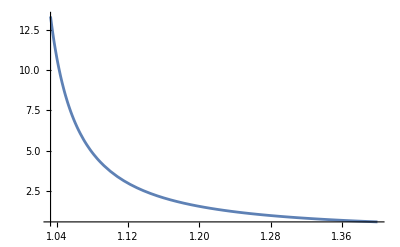

```mathematica
Plot[((2 vs)/((-1+vs) (1+vs))-Log[(1+vs)/(-1+vs)])/2,{vs,1.033,1.4},PlotRange->Full]
```

```mathematica
NSolve[SeriesCoefficient[F,{q,0,0}]==0,vs,Reals]
```

{{vs→-1.04438},{vs→1.04438}}

```mathematica
Solve[1/(2mx)==1/(2m0)+1/(2mstar)]
```

{{mx→(m0 mstar)/(m0+mstar)}}

```mathematica
mDOS=m0(mstar^2/(mstar^2-m0^2));
qprime=q √mDOS(Cos[θ] √((mstar+ σ m0)/(m0 mstar))+Sin[θ] √((mstar-σ m0)/(m0 mstar)))//Simplify
qratio=Assuming[m0>0&&mstar>0&&mstar>m0,Simplify[(qprime/.σ->-1)/(qprime/.σ->1)]]
```

√((m0 mstar^2)/(-m0^2+mstar^2)) q (√(1/m0+σ/mstar) Cos[θ]+√(1/m0-σ/mstar) Sin[θ])

(√(1/m0-1/mstar) Cos[θ]+√(1/m0+1/mstar) Sin[θ])/(√(1/m0+1/mstar) Cos[θ]+√(1/m0-1/mstar) Sin[θ])

√((-m0+mstar)/(m0+mstar))

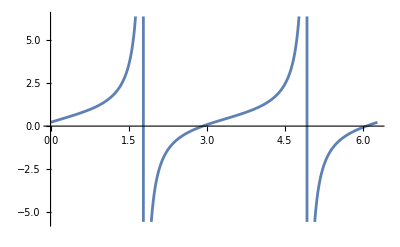

```mathematica
Assuming[m0>0&&mstar>0&&mstar>m0,Simplify[qratio/.θ->0]]
Plot[qratio/.{m0->1,mstar->1.1},{θ,0,2π}]
```

```mathematica
chiup=(+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)])/.{nuplus->vs+1/2 q,numin->vs-1/2 q};
Series[chiup,{q,0,1}]
```

1/2 (2-vs Log[(1+vs)/(-1+vs)])+O[q]^2

```mathematica
FΔ=
((1+σ)(1-z/2 Log[(z+1)/(z-1)])/.z->qratioabs vs )+(1-σ)(+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)])/.{nuplus->vs+1/2 q,numin->vs-1/2 q}//Simplify;
SeriesCoefficient[FΔ,{q,0,0}]//Simplify
Series[%,{vs,1,0}]//Simplify
vsΔ=SolveValues[Normal[%]==0,vs]//Simplify//Normal
vsΔ/.qratioabs->0
Series[vsΔ,{σ,0,1}]//Simplify
(1/(1-vs0[[1]])SeriesCoefficient[vsΔ,{σ,0,1}][[1]])//Simplify
(SeriesCoefficient[vsΔ,{σ,0,1}][[1]]/.qratioabs->0)//N
```

1/2 (4+vs (-1+σ) Log[(1+vs)/(-1+vs)]-qratioabs vs (1+σ) Log[(1+qratioabs vs)/(-1+qratioabs vs)])

1/2 (4-qratioabs Log[(1+qratioabs)/(-1+qratioabs)]-qratioabs σ Log[(1+qratioabs)/(-1+qratioabs)]-Log[2/(-1+vs)]+σ Log[2/(-1+vs)])+O[vs-1]^1

{1+2 ⅇ^(4/(-1+σ)) ((1+qratioabs)/(-1+qratioabs))^(-(qratioabs (1+σ))/(-1+σ))}

{1+2 ⅇ^(4/(-1+σ))}

{(1+(2 ((1+qratioabs)/(-1+qratioabs))^qratioabs)/ⅇ^4)+(4 ((1+qratioabs)/(-1+qratioabs))^qratioabs (-2+qratioabs Log[(1+qratioabs)/(-1+qratioabs)]) σ)/ⅇ^4+O[σ]^2}

4-2 qratioabs Log[(1+qratioabs)/(-1+qratioabs)]

-0.146525

```mathematica
F=
((1-z/2 Log[(z+1)/(z-1)])/.z->qratioabs vs )+(+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)])/.{nuplus->vs+1/2 q,numin->vs-1/2 q}//Simplify;
SeriesCoefficient[F,{q,0,0}]//Simplify
Series[%,{vs,1,0}]//Simplify
vs0=SolveValues[Normal[%]==0,vs]//Simplify//Normal
vs0/.qratioabs->0
```

1/2 (4-vs Log[(1+vs)/(-1+vs)]-qratioabs vs Log[(1+qratioabs vs)/(-1+qratioabs vs)])

1/2 (4-qratioabs Log[(1+qratioabs)/(-1+qratioabs)]-Log[2/(-1+vs)])+O[vs-1]^1

{1+(2 ((1+qratioabs)/(-1+qratioabs))^qratioabs)/ⅇ^4}

{1+2/ⅇ^4}

```mathematica
Series[vs0[[1]],{qratioabs,0,0}]
```

Piecewise[{{(1+2/ⅇ^4)-(2 ⅈ π qratioabs)/ⅇ^4+O[qratioabs]^2, Im[qratioabs]>0}, {(1+2/ⅇ^4)+(2 ⅈ π qratioabs)/ⅇ^4+O[qratioabs]^2, True}}]

```mathematica
SolveValues[%==qratioabs^-1,qratioabs]//Simplify
%[[1]]//N
```

!{Piecewise[{{(1+2/ⅇ^4)-(2 ⅈ π qratioabs)/ⅇ^4+O[qratioabs]^2, Im[qratioabs]>0}, {(1+2/ⅇ^4)+(2 ⅈ π qratioabs)/ⅇ^4+O[qratioabs]^2, True}}]}

SolveValues::nsmet: This system cannot be solved with the methods available to SolveValues.

$Aborted

Part::partd: Part specification $Aborted⟦1⟧ is longer than depth of object.

$Aborted⟦1⟧

```mathematica
Assuming[qratioabs>0,Solve[1/2 (4-vs Log[(1+vs)/(-1+vs)]-qratioabs vs Log[(1+qratioabs vs)/(-1+qratioabs vs)])==0,vs,Reals]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[1/2 (4-vs Log[(1+vs)/(-1+vs)]-qratioabs vs Log[(1+qratioabs vs)/(-1+qratioabs vs)])==0,vs,ℝ]

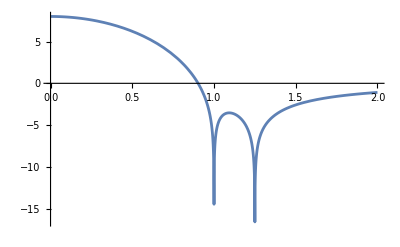

```mathematica
Plot[Re[ (8-2 vs Log[(1+vs)/(-1+vs)]-2 qratioabs vs Log[(1+qratioabs vs)/(-1+qratioabs vs)])/.qratioabs->0.8],{vs,0,2}]
```

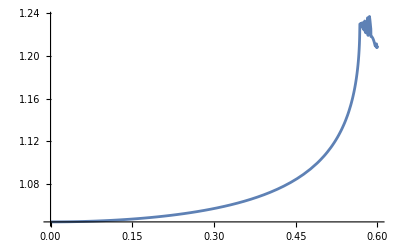

```mathematica
Plot[vs/.FindRoot[Re[1/4 (8-2 vs Log[(1+vs)/(-1+vs)]-2 qratioabs vs Log[(1+qratioabs vs)/(-1+qratioabs vs)])],{vs,1.1,1,1.5}],{qratioabs,0.,0.6}]
```

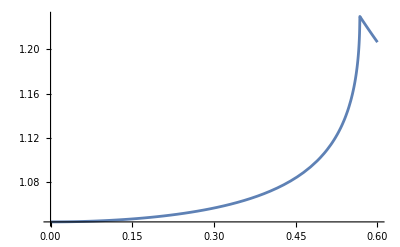

```mathematica
Plot[vs/.FindRoot[ (8-2 vs Log[(1+vs)/(-1+vs)]-2 qratioabs vs Log[(1+qratioabs vs)/(-1+qratioabs vs)])//Re,{vs,1.1,1.04,2}],{qratioabs,0.,0.6}]
```

```mathematica
Series[Re[1/4 (8-2 vs Log[(1+vs)/(-1+vs)]-2 qratioabs vs Log[(1+qratioabs vs)/(-1+qratioabs vs)])],{qratioabs,0,2}]//Simplify
```

Piecewise[{{1/4 (8+Re[-2 (vs Log[(1+vs)/(-1+vs)])-2 ⅈ π vs qratioabs-4 vs^2 qratioabs^2+O[qratioabs]^3]), Im[qratioabs vs (1+qratioabs vs)]≤0}, {1/4 (8+Re[-2 (vs Log[(1+vs)/(-1+vs)])+2 ⅈ π vs qratioabs-4 vs^2 qratioabs^2+O[qratioabs]^3]), True}}]

```mathematica
Limit[2 qratioabs vs Log[(1+qratioabs vs)/(-1+qratioabs vs)],qratioabs->0]
```

0

```mathematica
FindRoot[Re[1/4 (8-2 vs Log[(1+vs)/(-1+vs)])]/.qratioabs->0,{vs,1.1}]
```

{vs→1.04438}

```mathematica
Series[q^-2/(1+q^-2),{q,0,2}]
```

1-q^2+O[q]^3

```mathematica
N[(2+ⅇ^4)/ⅇ^4]
```

1.03663

```mathematica
NSolve[(1/4 (8-2 vs Log[(1+vs)/(-1+vs)]-2 qratioabs vs Log[(1+qratioabs vs)/(-1+qratioabs vs)])==0)/.qratioabs->0.1,vs,Reals]
```

{}

```mathematica
|
```

```mathematica
Series[2-1/2 vs Log[(1+vs)/(-1+vs)],{vs,1,0}]
```

1/2 (4-Log[2/(-1+vs)])+O[vs-1]^1

```mathematica
Solve[1/2 (4-Log[2/(-1+vs)])==0]
```

{{vs→(2+ⅇ^4)/ⅇ^4}}

```mathematica
Exp[-4]//N
```

0.0183156

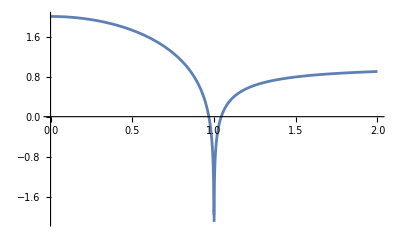

```mathematica
Plot[Re[2-1/2 vs Log[(1+vs)/(-1+vs)]],{vs,0,2}]
```

```mathematica
F=
(1+1/2-(1-(numin)^2)/(4q)Log[(numin+1)/(numin-1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)])/.{nuplus->vs+vs2 q+1/2 q,numin->vs+ vs2 q-1/2 q};
Solve[SeriesCoefficient[F,{q,0,2}]==0,vs2]
```

{{vs2→-ⅈ/(2 √3)},{vs2→ⅈ/(2 √3)}}

```mathematica
|
```

{{vs2→(1/2+1/4 (1+ⅈ η) Log[-(ⅈ (2+ⅈ η))/η]+1/4 (1+ⅈ η) Log[-(ⅈ η)/(2+ⅈ η)])/(1-1/2 (1+ⅈ η) Log[-(ⅈ (2+ⅈ η))/η]+1/2 (1+ⅈ η) Log[-(ⅈ η)/(2+ⅈ η)])}}

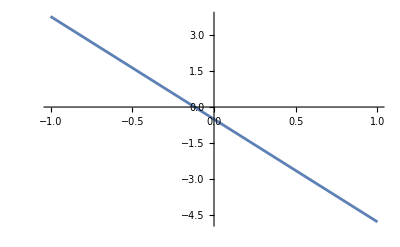

```mathematica
F=
(-1+1/2-(1-(numin)^2)/(4q)Log[-(numin-1)/(numin+1)]+(1-(nuplus)^2)/(4q)Log[(nuplus+1)/(nuplus-1)])/.{nuplus->vs+vs2 q+1/2 q,numin->vs+vs2 q-1/2 q};
Solve[(SeriesCoefficient[F,{q,0,0}]/.vs->1+η ⅈ)==0,vs2]
Plot[Re[SeriesCoefficient[F,{q,0,0}]/.vs->1+10^-2 ⅈ],{vs2,-1,1}]
```

```mathematica
Limit[(-3/2+1/4 (1+ⅈ η) Log[-(ⅈ (2+ⅈ η))/η]+1/4 (1+ⅈ η) Log[-(ⅈ η)/(2+ⅈ η)])/(1-1/2 (1+ⅈ η) Log[-(ⅈ (2+ⅈ η))/η]+1/2 (1+ⅈ η) Log[-(ⅈ η)/(2+ⅈ η)]),η->0,Direction->"FromAbove"]
```

0

```mathematica
F=Series[
-1+1/2-(1-(vs-1/2 q)^2)/(4q)Log[-(vs-1/2 q-1)/(vs-1/2 q+1)]+(1-(vs+1/2 q)^2)/(4q)Log[(vs+1/2 q+1)/(vs+1/2 q-1)]
,{q,0,-1}]//Simplify
Solve[F==0//Normal,vs]
```

((-1+vs^2) (Log[-(-1+vs)/(1+vs)]-Log[(1+vs)/(-1+vs)]))/(4 q)+O[q]^0

{{vs→-ⅈ},{vs→ⅈ}}

```mathematica
Series[
-1+1/2-(1-(vs+vs2 q-1/2 q)^2)/(4q)Log[-(vs+vs2 q-1/2 q-1)/(vs+vs2 q-1/2 q+1)]+(1-(vs+vs2 q+1/2 q)^2)/(4q)Log[(vs+vs2 q+1/2 q+1)/(vs+vs2 q+1/2 q-1)]
,{q,0,1}]//Simplify
```

((-1+vs^2) (Log[-(-1+vs)/(1+vs)]-Log[(1+vs)/(-1+vs)]))/(4 q)+1/4 (-2+4 vs2+vs (-1+2 vs2) Log[-(-1+vs)/(1+vs)]-(vs+2 vs vs2) Log[(1+vs)/(-1+vs)])+1/16 ((4 (vs+4 vs vs2^2))/(-1+vs^2)+(1-2 vs2)^2 Log[-(-1+vs)/(1+vs)]-(1+2 vs2)^2 Log[(1+vs)/(-1+vs)]) q+O[q]^2

```mathematica
Solve[(-1+vs^2) (Log[-(-1+vs)/(1+vs)]-Log[(1+vs)/(-1+vs)])==0,vs]
```

{{vs→-ⅈ},{vs→ⅈ}}

```mathematica
Solve[1/4 (-2+4 vs2+vs (-1+2 vs2) Log[-(-1+vs)/(1+vs)]-(vs+2 vs vs2) Log[(1+vs)/(-1+vs)])==0,vs]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[1/4 (-2+4 vs2+vs (-1+2 vs2) Log[-(-1+vs)/(1+vs)]-(vs+2 vs vs2) Log[(1+vs)/(-1+vs)])==0,vs]